# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-17);
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/niels/Projects/Johannes/He_E1

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v24/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
(*SetDirectory[resultsDir]*)
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

Import::nffil: File ../../../data/he3_photo_diss_sigma_golak.dat not found during Import.

Import::nffil: File ../../../data/he3_photo_diss_sigma_gibson.dat not found during Import.

Part::partw: Part 2 of Transpose[$Failed] does not exist.

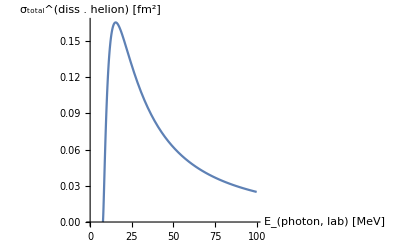

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

```mathematica
MinMax[Eigenvalues[He3Norm]]
```

{2.91522×10^-14,481103.}

Bad! so He3 eigenvalue will be spurious--or at least run the risk.

```mathematica
dg=Table[He3Norm[[i,i]],{i,1,Length[He3Norm]}];Take[dg,4]
```

{3.80389×10^-6,7.55471×10^-6,0.0000144861,0.0000272183}

So states are not normalised; start by fixing that

```mathematica
regHe3=DiagonalMatrix[1/Sqrt[dg]];
```

```mathematica
He3Norm=regHe3.He3Norm.regHe3;He3Ham=regHe3.He3Ham.regHe3;
```

```mathematica
MinMax[Eigenvalues[He3Norm]]
```

{2.07697×10^-10,72.4624}

#### The initial state (helion ground state ^3 He ) -- in bare RGM Basis

B(^3He) = -6.10783

Dim_full^helion = 432

{0,0}

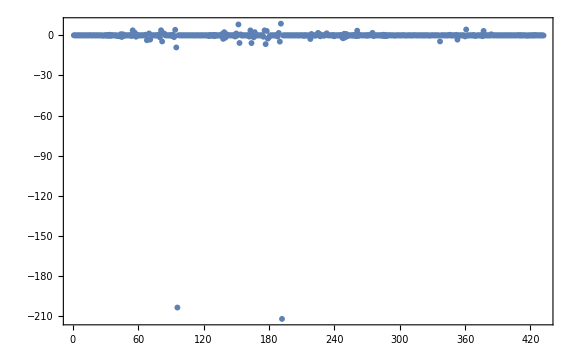
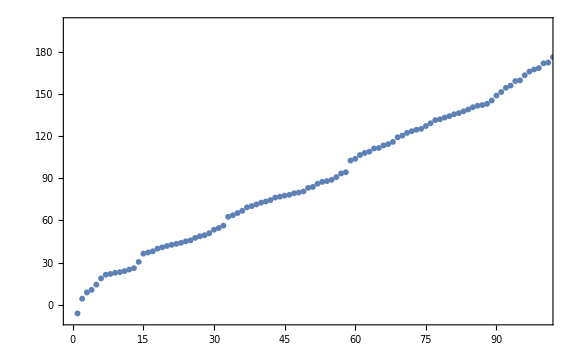
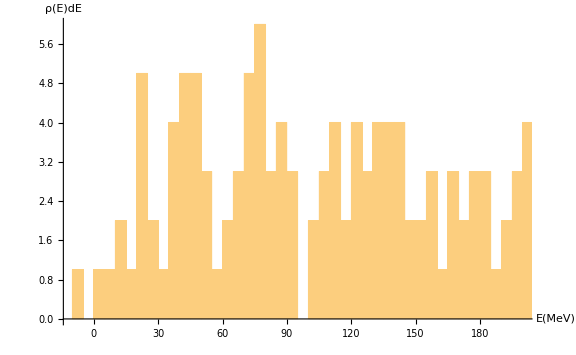
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVbare=Sort[Transpose[Eigensystem[{He3Ham,He3Norm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0bare,v0bare}=orderedEVbare[[1]];
v0bare=v0bare/Sqrt[v0bare.He3Norm.v0bare];
dE=5;
Print["B(^3He) = ",e0bare];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]]];
Print[MinMax[Im[v0bare]]];
Grid[{{
ListPlot[Re[v0bare],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVbare[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVbare[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E(MeV)","ρ(E)dE"}]
}}]
```

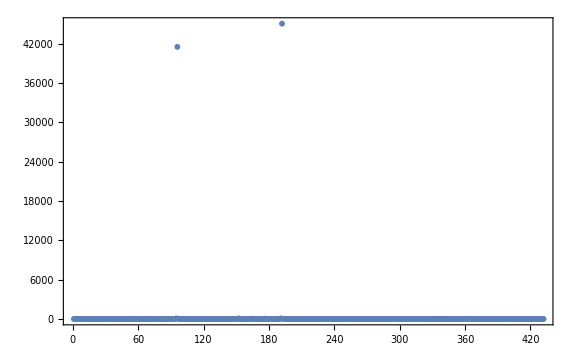

```mathematica
ListPlot[Abs[v0bare]^2,PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle^2",Magnification->2]},ImageSize->Large]
```

OK, not good. Looks there is some nonsense here

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
thresholdLIT=10.^-8
```

1.×10^-8

```mathematica
SymmetricMatrixQ[He3Norm]
```

True

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {2.07697×10^-10,72.4624}

(min/max) discarded elements: 10 {2.07697×10^-10,7.82664×10^-9}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -6.10367

Part::partw: Part 1 of {} does not exist.

Dim_full^helion = 432=^!432   ;     Dim_(non - singular)^helion = {}⟦1⟧

Norm=1.

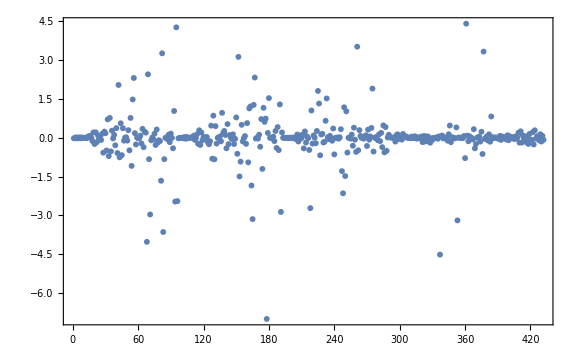
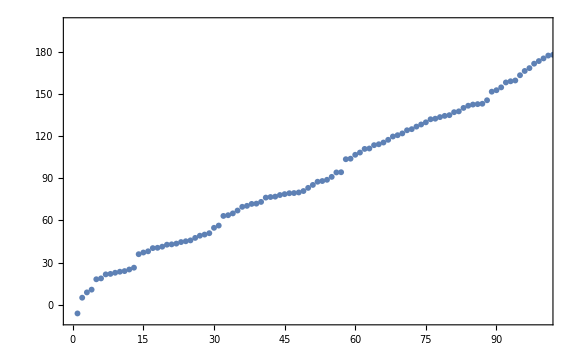
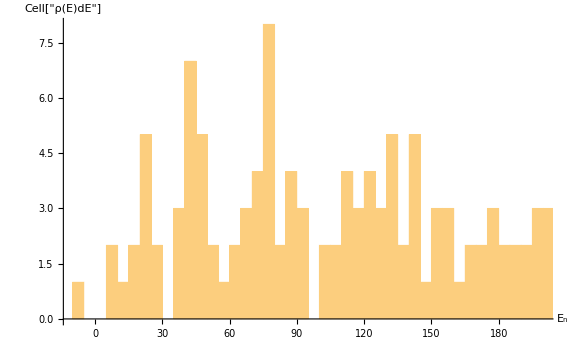
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
```

N_final = {767}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

```mathematica
MinMax[Eigenvalues[LitNorm[[1]]]]
```

{6.94365×10^-10,3.85276×10^9}

Bad! so He3 eigenvalue will be spurious--or at least run the risk.

So states are not normalised; start by fixing that

```mathematica
MinMax[Eigenvalues[He3Norm]]
```

{2.07697×10^-10,72.4624}

J=0.5:  E_0=-1.32497

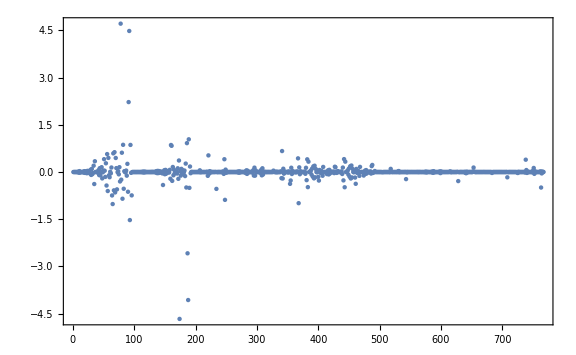
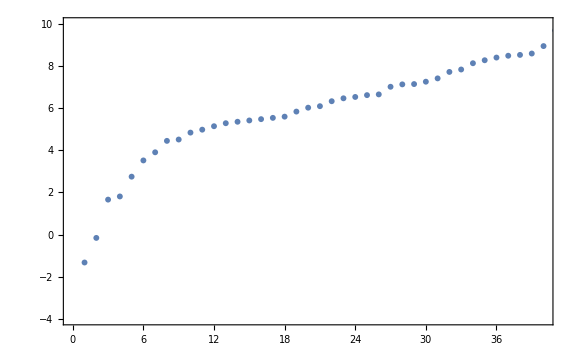
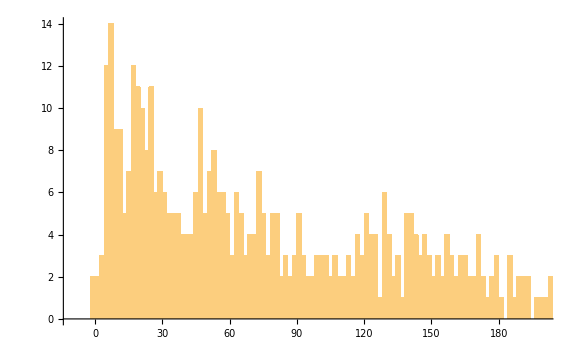
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
dE=2.;regLIT={};
Do[dg=Table[LitNorm[[1,i,i]],{i,1,Length[LitNorm[[nj]]]}];reg=DiagonalMatrix[1/Sqrt[dg]];AppendTo[regLIT,reg];LitNorm[[nj]]=reg.LitNorm[[nj]].reg;LitHam[[nj]]=reg.LitHam[[nj]].reg;
orderedEVbareOut=Sort[Transpose[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0l,v0l}=orderedEVbareOut[[1]];v0l=v0l/Sqrt[v0l.LitNorm[[nj]].v0l];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
Print[Grid[{{
ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[1]]&/@orderedEVbareOut,PlotRange->{{0,40},{-4,10}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[1]]&/@orderedEVbareOut,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]],{nj,Range[1,Length[Subscript[I, n]]]}];
```

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in Norm-Eigen-Vector Basis

Final-state Basis dimension = {767}

min/max: {3.33414×10^-9,45.5671}

(min/max) discarded elements: 10 {3.33414×10^-9,8.72656×10^-8}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

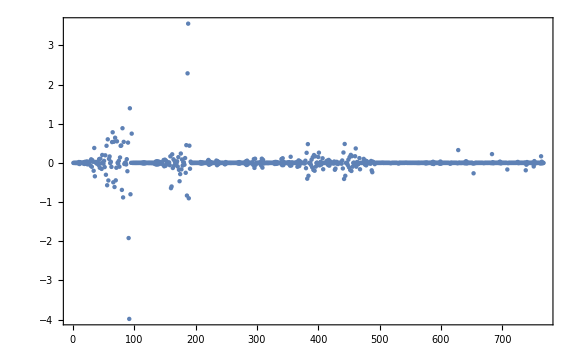
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
thresholdLIT=10.^-7;dE=2.;
Do[
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[1]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]].v0l];
Print[Grid[{{
ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[1]]&/@orderedEVbareOut,PlotRange->{{0,40},{-4,10}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[1]]&/@orderedEVbareOut,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]],{nj,Range[1,Length[Subscript[I, n]]]}];
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt;
tmp =BinaryReadList[fntmp,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
Print[Dimensions[tmp][[1]]];
test=regLIT[[nj]].ArrayReshape[tmp,{OutDim,He3BasisDim}].regHE3;
AppendTo[CouplingBlockT,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

331344

331344

Dim(⟨ψ|ο̂|helion⟩) = {1,767,432}

Dim(⟨ψ|Ĥ|ψ⟩) = {1,767,767}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1,767,767}

```mathematica
Dimensions[CouplingBlockj[[1]][[2]][[2]]]
```

{767,432}

```mathematica
Dimensions[CouplingBlockj]
```

{1,2,2}

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-6.10083 norm=1.

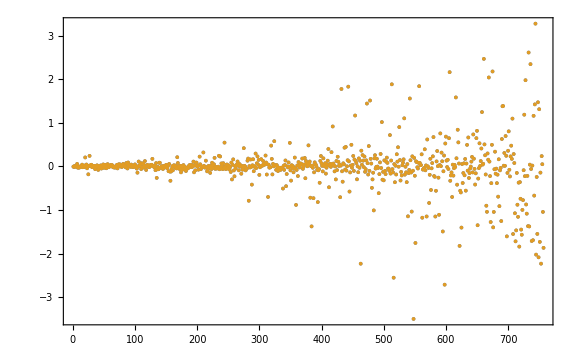

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB;tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];Print[ListPlot[inhomoEB[[1]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]]
,{nj,Range[1,Length[Subscript[I, n]]]}
];
```

That looks rather dodgy! Is the normalisation consistent?

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
```

```mathematica
EvalGSiEV
```

-6.10083

Check

```mathematica
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

{1.,-6.10083}

```mathematica
lpsisEV[[1]]
```

{7948.87,3.4904×10^-7}

E_0^initial = -6.10083    dim(initial) = {407}

E_0^final  = -1.32485    dim(final)   = {757}

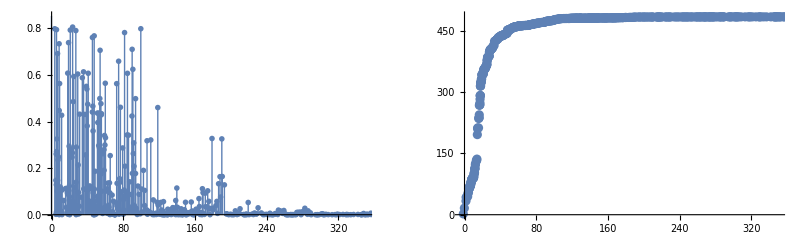

```mathematica
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]])).OμLHSEV;(tmp+Transpose[tmp])/2];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockj[[nj]][[mm]][[2]].EvecGSiEV);
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];
CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];
Print[GraphicsRow[{
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,350},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
,
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
},ImageSize->Full]]

,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

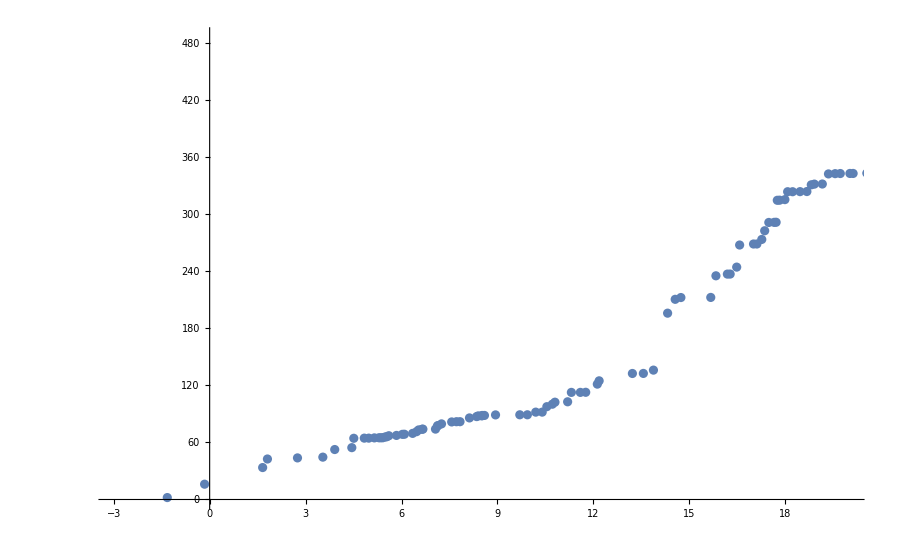

```mathematica
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,20},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
```

```mathematica
EvecsFEV[[4]]
```

{-0.000218885,-0.0638661,-0.0585182,-0.0130136,0.000168519,-0.00019622,-0.00659899,0.000248919,-0.0059622,0.000164091,0.0111313,0.0000522454,1.35649×10^-6,0.0000940174,-0.110594,0.0000228423,-0.0963754,0.0000343926,-0.000142712,0.0290653,-0.000114026,-0.00382742,-0.000157676,0.0000289166,-0.0358137,-0.0194861,-0.0128023,-0.000429204,-0.000204674,-0.0000883679,0.000410345,-0.0278894,0.0000626876,0.0122596,-0.000037001,-0.000140481,-0.000149603,0.0000115001,0.000362684,-0.159953,-0.0000279914,0.111288,-0.048865,-0.000315977,-0.0303534,0.019516,-0.0000479693,0.0000710319,-0.000133186,0.0000649376,-0.0757523,0.0000822687,0.00494092,-0.0263185,0.0000130971,-0.0000490595,-0.0000906505,-0.000357715,0.0285264,-0.0171535,-0.000160217,0.0000482656,-6.8891×10^-6,-0.00948036,0.000218373,-0.000231813,-0.0247908,-2.97443×10^-6,0.0368922,-0.0000618379,-0.0218159,0.0000970528,0.00227735,0.00437101,-0.155927,0.000124363,-0.000113086,-0.150443,-0.00019283,0.139685,0.000277979,0.000394746,-0.0000190678,4.70308×10^-6,0.0000891939,-0.000167739,-0.0394041,0.000116314,-0.0070778,0.0449134,-0.000182881,0.0190419,-0.0000144708,0.0000950329,-0.000149711,0.0131169,-0.0000216506,-0.0000734493,-0.0000185134,0.038213,0.000157213,-0.0000204756,-0.0109688,0.00581746,-0.044365,0.00025664,-0.0000687937,-0.0000297075,0.0311155,0.0000921118,0.00558901,0.0000431347,0.0512327,-0.000288041,0.000192455,7.48606×10^-6,-0.229102,0.0000256321,-0.0805388,-0.000646859,0.0000423308,0.108221,-0.000135284,0.040565,0.0000651715,-0.0203418,-0.00010642,0.056605,-0.0000261757,0.00612489,0.0000560022,8.70576×10^-6,0.00277706,0.000109811,0.00604658,-0.00017949,0.0000476469,-0.0379808,0.000174794,0.00314884,0.0307872,-0.000182191,0.0000391736,0.00685989,0.000375236,-2.56137×10^-6,0.000047375,-0.0398684,-0.0000639547,-0.000138925,-0.0894555,-0.0000311931,0.0000380212,0.0414256,-0.000269217,0.000177287,0.0200001,-0.00029984,-0.000105116,-0.0292546,-0.0158337,-0.0000158479,-4.56152×10^-6,0.0178911,0.0150431,-0.000125675,0.000110132,-0.0450452,0.000243872,-0.119764,-0.000206207,-0.0205642,-0.0000545771,0.000454821,0.194525,0.0480844,0.0000166102,-0.0000284013,0.0000374869,-0.141625,-6.32482×10^-7,-0.000171755,-0.000125866,0.000490927,0.0000808514,-0.0000376525,-0.000296061,0.0300499,-0.0000457208,-0.01018,0.0000174758,0.000020556,-0.0405077,-0.0164692,0.0270899,-8.73072×10^-6,0.000243833,0.0416055,0.000753927,0.0000189987,0.0000615197,0.0637329,-0.00407142,0.00551669,0.105459,0.000207121,0.000303884,3.72994×10^-6,-0.000141056,0.0294671,-0.0000261875,-0.0498402,-0.0000327548,0.0394208,0.000140073,-0.000200595,-0.00335939,0.000173715,0.0000315685,-0.000348196,-0.0000606927,0.0000165607,0.0000840248,0.0123526,0.000400371,0.0727176,-0.0000144911,-7.59001×10^-6,-0.0631826,0.000231015,0.0000521114,0.175861,0.00809401,-0.0000211443,-0.0312487,-0.0000785867,-0.0513251,-0.0000449206,0.000332133,0.0120125,-0.000357399,-0.112537,-0.0000821307,0.0283078,-0.0000107218,0.000435269,0.000267964,2.85945×10^-6,0.115511,0.0227081,0.000205118,0.000367251,-0.000072628,-0.0301995,-0.000155547,0.0221003,-0.000117216,0.0939912,0.0011664,0.04307,0.0000875533,0.0000161018,0.0000227241,-0.011229,-0.00026958,0.0000345294,-0.0000366501,-0.0000252883,0.0729102,7.31997×10^-6,-0.00502912,0.000470791,-0.0000366064,-0.0998539,0.00743662,-0.000112568,0.0198404,3.72442×10^-7,-0.000205452,-0.000166937,0.000166559,-0.0102111,0.0426887,0.000120307,-0.000181592,-0.101001,-0.0000675926,-0.0210701,0.0000498771,-0.0000599201,0.000146367,-0.000207813,-0.0000586655,0.00490882,-0.0761867,0.0000575637,0.0603891,0.000221647,-0.0423216,0.000112514,3.73417×10^-7,0.1258,0.0583918,0.000168984,-0.0000131324,0.0888296,-0.0000785117,-0.0000263037,0.000423159,0.0110065,-0.000190841,-0.0648763,0.000325877,-0.0264795,0.0000705201,-0.000274657,-0.0000307521,0.000380627,0.0223458,0.0397403,0.0545781,-0.000124919,0.0000404091,0.0403434,-8.63908×10^-6,0.000100816,-0.0000578735,0.109608,-0.0000347528,-0.0206316,1.00946×10^-6,0.000048663,-0.0105878,0.109501,-0.0000472006,0.000196207,-0.0000825742,0.00475695,0.000117187,-0.00938124,-0.0000383264,0.000102461,0.0236598,0.0353924,0.000268712,-0.0000264104,0.0000631181,-0.000278413,-0.0462946,0.0908434,0.016555,-5.16083×10^-6,-0.0000342382,-0.0000132798,0.0000810514,0.0000628138,-0.00347355,-0.115951,0.0264067,-0.000264477,-0.000418478,-0.00637784,0.0884777,0.000050598,-9.78818×10^-6,-0.0506926,0.0000147128,-0.0269983,0.0000396461,0.0000887017,0.0000573712,-0.0000182737,0.00843642,-0.00773887,0.0000536256,-0.0000511716,-0.0496547,0.000032103,-0.0155077,0.000393857,-0.000211016,0.0662699,-0.0000879749,-0.0684035,-0.0000763366,0.0000189124,-0.00454635,-0.000205949,-0.0688244,-0.000137083,-0.0000845845,-0.000179152,0.144066,0.00479446,0.0000214993,0.000117687,0.0237114,-0.0000234122,0.0081435,-1.94119×10^-6,-0.0000260942,-0.0261056,0.0352716,7.48618×10^-6,0.000249293,0.101496,-0.0000516687,0.000036581,0.000265488,0.0000175318,-0.0269862,-0.0513817,-0.0205213,-0.000142328,-0.0000740385,0.0188305,-4.41822×10^-6,0.0173885,-0.0536493,-0.0000394223,-0.000168422,0.000047765,-0.00112245,-0.0000754147,-0.000132619,0.046006,0.000293203,-0.0294527,-0.0000165411,-0.0703017,0.0000444683,-0.0334513,-0.000104013,0.000666869,0.0000610241,-0.0000300898,-0.0189461,0.000273312,-0.00688522,-0.0308249,0.000109172,-0.0000265679,-0.105303,-0.000135508,-0.129878,0.000176896,0.00013898,0.0587631,-0.00029485,0.000156556,-0.0072561,-0.0000909023,-1.4118×10^-6,0.0461258,-0.0000417496,-0.00017502,0.058968,0.132699,-0.0000331524,0.0000417345,0.0000194096,-0.000263564,-0.0145404,-0.0000909299,0.0000384969,-0.00531819,-0.0000926398,0.000140492,0.0696438,-0.000125267,-0.0149969,0.0000266082,-0.0156163,-0.0000987236,0.0000408096,0.00131398,0.000168676,0.018672,-0.00206872,-0.000119368,0.0299007,-0.000301625,0.0000713423,0.0669355,-0.0000607544,-0.0393959,-0.0337078,0.0000838497,0.0000836397,-0.00018125,0.00011675,-0.051724,-0.000198164,8.68151×10^-6,-0.000843096,-0.000166948,0.0346248,0.000178195,0.120686,0.0537543,-0.0000244698,-0.0420172,-0.0000273534,0.0691072,0.0000224804,0.0834799,-0.0000324365,-0.0000149387,-0.000016558,-0.0445945,-0.000193458,-0.000213541,0.0114126,-0.000104228,-0.0000979389,0.0560067,-0.000175259,-0.096446,0.00520108,-0.0000988012,-0.0000482543,0.0000546951,0.0785844,-0.0000101711,-0.00192984,0.0000772101,0.0315645,0.00018452,0.0000708443,0.0000267488,-0.0000403962,-0.0618423,-0.00533757,0.0000622898,0.000166829,0.0000106123,-0.0443734,-0.0000937319,0.040488,0.0609749,-0.000274907,0.0031437,0.000128444,0.0000666445,0.0481442,-0.000223244,0.000182639,-0.0306167,0.0000332938,0.0000666849,0.012794,8.56167×10^-7,0.0000887947,-0.000138904,-0.0836627,-0.0000322334,0.0811189,-0.0214347,0.000109167,-0.0482681,0.131547,0.0277658,-0.0000687903,0.000101646,-0.00001023,-0.0000951583,0.000134983,-0.0000969368,-0.0161194,-0.0578469,0.0000297006,-0.000167331,-0.0416947,0.00749014,0.000167525,-0.0691785,0.0000213027,-0.0000850461,0.000060098,-0.00469062,0.00017875,0.000086934,0.0479915,-0.0000892231,0.0000189874,0.0000186743,-8.93096×10^-6,-0.000162786,0.0263944,-0.0317068,-0.000111644,-0.0000430708,0.137913,-0.0000556906,0.0300319,-0.0000469658,-0.0398893,-0.0406508,0.0000777306,0.0795036,0.000203312,-0.0000846567,-0.0000385006,0.000216934,-0.0346529,-0.0385087,-0.000194207,0.00335071,-0.0000229036,-0.074865,-0.0000550492,0.000175912,-0.0759094,0.0000277283,0.000125123,-0.0495937,0.0000977922,0.0258912,-0.0000504014,0.0284487,-0.00019119,0.00831811,-5.68125×10^-6,0.0180917,-0.0672131,0.0000926279,-0.0234685,0.0000673017,-0.0000851084,0.0000611491,0.000133083,-0.0000476373,-0.0295527,7.60925×10^-6,-0.000192806,0.0000413194,-0.124851,0.0000103681,-1.75308×10^-6,0.0298237,-0.0000512884,-0.0000329874,-0.0283592,-0.0684943,-0.0000424065,-8.32907×10^-6,-0.000144507,0.0584662,-0.0425061,0.0000821296,0.0510454,0.0686304,-0.0000701355,0.000083007,-0.000255958,-0.0373634,-0.000173108,-0.0413958,0.0000453321,-9.35902×10^-6,-0.0382818,-0.0000761119,0.000133388,-0.0267779,0.0000639587,-0.0296293,0.000105912,-0.000155546,0.0428452,0.00871984,-0.0000302625,0.0000373577,0.000105953,-0.0000108721,0.0409517,0.122485,-0.0000238365,0.00016612,-0.0000163642,0.0381175,-0.000071984,-0.0191214,-0.00011683,-0.00310487,0.0000202745,0.0742587,-0.000117422,0.0000287521,-0.0673841,0.0326415,-0.0000734482,0.00677339,0.000182433,-0.000438521,0.0000152221,-0.0000655186,2.3021×10^-6,-0.0165001,0.0000402939,-0.000176344,0.0527801,3.47885×10^-6,-0.0195442,0.0000719049,0.0000380997,-0.000189161,0.0969226,0.0587358,0.0000259277,0.0000446148,0.0187846,-0.0000249314,-0.0000668308,0.0000394872,-0.0223531,0.0358923,0.000142506,-0.0339908,-0.000114638,-0.0599433,-0.00003207,-0.022198,-0.0000102036,1.86644×10^-6,-0.000109654,-0.0101603,-0.0730593,0.000179784,-0.00269761,-0.0000433554,6.90256×10^-6,0.0000135829,-0.0385434,0.00999067,0.0000674903,-0.000112875,-0.0317853,0.0000173321,-0.000138832,0.00405568,-0.0000667372,-0.0392334,-0.0357417,0.00544722,-8.43143×10^-6,0.000044706,-0.0182037,-0.000144083,-0.0000844824,-0.0000618942,-0.0121382,-0.000079784,0.0239372,-0.0000362088,0.000031608,-0.0000893981,-0.0105291}

Let us investigate the structure of the LIT Norm matrix

```mathematica
pos=Flatten[Position [LitNorm[[1,1]],0.]];cumul=Transpose[{pos,Join[{0},Differences[pos]]}];cs=SequenceSplit[cumul,{a_/;a[[2]]>1,b__}:>{a,b}];{#[[1,1]],#[[-1,1]]}&/@ cs
```

{{193,252},{313,767}}

```mathematica
zerob=Table[pos=Flatten[Position [LitNorm[[1,i]],0.]];cumul=Transpose[{pos,Join[{0},Differences[pos]]}];cs=SplitBy[cumul,#[[2]]>1&];l@@({#[[1,1]],#[[-1,1]]}&/@ cs),{i,1,Length[LitNorm[[1]]]}]
```

{l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],l[{193,252},{313,313},{314,547},{603,603},{604,767}],748,l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}],l[{1,432},{493,493},{494,657}]}
 |  |  |  |

```mathematica
zerob=zerob//.l[s___,{a_,a_},{b_,c_},e___]->l[s,{a,c},e]
```

{l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],l[{193,252},{313,547},{603,767}],737,l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}],l[{1,432},{493,657}]}
 |  |  |  |

```mathematica
nzeron=zerob/.{l[{a_,b_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,c-1},If[d<767,{d+1,767},Null]},Null],l[{a_,b_},{b1_,c1_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,b1-1},{c1+1,c-1},If[d<767,{d+1,767},Null]},Null],l[{a_,b_},{b1_,c1_},{b2_,c2_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,b1-1},{c1+1,b2-1},{c2+1,c-1},If[d<767,{d+1,767},Null]},Null],l[{a_,b_},{b1_,c1_},{b2_,c2_},{b3_,c3_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,b1-1},{c1+1,b2-1},{c2+1,b3-1},{c3+1,c-1},If[d<767,{d+1,767},Null]},Null]};
```

```mathematica
ls=Union[Flatten[nzeron,1]]
```

{{1,192},{193,252},{253,312},{313,432},{433,492},{493,547},{548,602},{603,657},{658,767}}

```mathematica
LitNorm[[1,{313,314}]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.960675,-0.960729,-0.781707,-0.569834,-0.402118,-0.28127,-0.195346,-0.134549,-0.0919701,-0.0625037,-0.0423136,-0.0285753,-0.616596,-0.658407,-0.615773,-0.474839,-0.320993,-0.21064,-0.139834,-0.0940584,-0.0636264,-0.0430611,-0.0291033,-0.0196404,-0.281858,-0.280691,-0.264703,-0.232031,-0.176693,-0.11631,-0.0729464,-0.046555,-0.0305307,-0.0203682,-0.0136882,-0.00921863,-0.108982,-0.101843,-0.0892383,-0.0756082,-0.0625077,-0.0479384,-0.0320761,-0.0197583,-0.0122363,-0.00784053,-0.00516166,-0.00344654,-0.0384461,-0.0346889,-0.0289354,-0.0229756,-0.0179623,-0.0141223,-0.0108852,-0.00759471,-0.00473078,-0.00287268,-0.0017994,-0.00116709,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.970157,0.888606,0.765837,0.616551,0.465066,0.334189,0.233167,0.160071,0.108934,0.0737769,0.0498298,0.813258,0.736709,0.622776,0.506252,0.400654,0.306923,0.225616,0.15973,0.11033,0.0752183,0.0509559,0.0344119,0.448469,0.400547,0.322467,0.243953,0.180896,0.134326,0.0994987,0.0722819,0.051019,0.0351753,0.0239321,0.0161833,0.186774,0.168185,0.135807,0.100231,0.0702504,0.0488249,0.0345621,0.02494,0.0180024,0.0127485,0.00882172,0.00601057,0.0671633,0.0601535,0.0490087,0.036725,0.0256838,0.0172078,0.0114597,0.00781741,0.00550727,0.00394777,0.00280987,0.0019585,0.0958536,0.0993491,0.0885446,0.0669687,0.0439259,0.0262973,0.0149085,0.00816247,0.00436917,0.00230583,0.00120645,0.000627986,0.0590772,0.0588808,0.0492312,0.0362646,0.0239465,0.0142755,0.00796916,0.0043119,0.00229443,0.0012076,0.000630983,0.000328199,0.0211798,0.0208925,0.0171741,0.0120105,0.00762057,0.00457298,0.0025844,0.00138923,0.000731244,0.000382507,0.000199365,0.000103594,0.00567371,0.00537868,0.00434326,0.00303976,0.00188043,0.00107945,0.000605972,0.000332788,0.000176148,0.0000913488,0.0000472651,0.0000244832,0.00132603,0.00120862,0.00093966,0.000643646,0.000401009,0.000230685,0.000125127,0.0000670513,0.000036113,0.0000190732,9.84047×10^-6,5.05522×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0500811,0.0344922,0.0201255,0.0103353,0.00481841,0.00210586,0.00088478,0.000363141,0.00014699,0.0000590096,0.0000235743,0.0335807,0.0226276,0.01256,0.00621025,0.00286233,0.00124921,0.000524121,0.000214696,0.000086763,0.0000347939,0.0000138909,0.0189377,0.0150571,0.00987552,0.00549359,0.00265021,0.00117762,0.000506688,0.000212964,0.0000874796,0.00003537,0.000014178,0.00737705,0.00558882,0.00345449,0.00185269,0.000902789,0.000402675,0.000168431,0.0000693141,0.0000284683,0.0000115744,4.65268×10^-6,0.00254213,0.00185685,0.00111251,0.000573278,0.000268572,0.000119907,0.0000513357,0.0000209088,8.366×10^-6,3.37721×10^-6,1.36561×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0890661,-0.0634452,-0.0368605,-0.0185256,-0.00851987,-0.00370627,-0.00155568,-0.000638477,-0.000258465,-0.000103771,-0.0000414586,-0.0593283,-0.0399391,-0.0230146,-0.0115394,-0.00521961,-0.0022339,-0.000929014,-0.000379584,-0.00015332,-0.000061482,-0.0000245465,-0.034577,-0.0279033,-0.0178764,-0.00970142,-0.00479298,-0.00219633,-0.000938333,-0.000385463,-0.000156103,-0.0000627976,-0.0000251402,-0.0130919,-0.010143,-0.00642276,-0.00342555,-0.00161306,-0.000718378,-0.000311463,-0.000129662,-0.0000521963,-0.0000208054,-8.28927×10^-6,-0.00447421,-0.00329418,-0.00200556,-0.00105955,-0.000502258,-0.00021838,-0.0000911551,-0.0000380226,-0.0000156646,-6.26983×10^-6,-2.47727×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.933624,-0.992003,-0.853289,-0.650746,-0.474704,-0.339626,-0.23934,-0.166358,-0.114345,-0.0779696,-0.0528889,-0.0357593,-0.647156,-0.735168,-0.726652,-0.585483,-0.40852,-0.273842,-0.184284,-0.125008,-0.0849979,-0.0577025,-0.0390705,-0.0263956,-0.312701,-0.331405,-0.329933,-0.301644,-0.236667,-0.15891,-0.100927,-0.0649148,-0.042772,-0.0286155,-0.0192631,-0.0129861,-0.125252,-0.124497,-0.114959,-0.101365,-0.0861698,-0.0673068,-0.0455589,-0.0282632,-0.0175786,-0.0112926,-0.00744561,-0.00497608,-0.0452219,-0.0433496,-0.0380222,-0.0313444,-0.0251461,-0.0201055,-0.0156611,-0.0109975,-0.00687705,-0.00418567,-0.00262545,-0.00170426,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.970157,1.,0.9684,0.873307,0.726907,0.560911,0.409024,0.288006,0.198827,0.135765,0.092133,0.062302,0.852214,0.821321,0.733875,0.623445,0.509362,0.398646,0.297087,0.212126,0.147281,0.100723,0.06836,0.0462162,0.496876,0.472311,0.401481,0.316848,0.242113,0.18341,0.137591,0.10074,0.071444,0.0493977,0.0336655,0.0227881,0.214407,0.205376,0.174794,0.134281,0.0967919,0.0685235,0.049074,0.0356659,0.0258561,0.0183576,0.0127226,0.00867632,0.0789158,0.0751003,0.0643502,0.0500736,0.0359413,0.0244912,0.0164842,0.0113182,0.00800481,0.00575151,0.0040994,0.00285967,-0.0435977,-0.0447891,-0.0396302,-0.0298158,-0.0194876,-0.0116405,-0.0065901,-0.00360506,-0.00192873,-0.00101758,-0.000532323,-0.000277058,-0.0356441,-0.0351597,-0.0291506,-0.0213409,-0.0140334,-0.00834364,-0.00465007,-0.00251349,-0.00133666,-0.000703255,-0.000367381,-0.000191065,-0.0154984,-0.0151193,-0.012318,-0.00855886,-0.005407,-0.00323565,-0.00182547,-0.000980247,-0.000515646,-0.000269629,-0.000140501,-0.0000729979,-0.0045968,-0.00430898,-0.00344872,-0.00239842,-0.00147742,-0.000845832,-0.000474038,-0.000260071,-0.000137575,-0.0000713197,-0.000036894,-0.0000191086,-0.00112471,-0.00101385,-0.000781518,-0.000532107,-0.000330204,-0.000189477,-0.000102617,-0.0000549376,-0.0000295721,-0.0000156134,-8.05389×10^-6,-4.13694×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0238199,-0.01729,-0.0105122,-0.00555923,-0.00264289,-0.0011695,-0.000495147,-0.00020417,-0.0000828733,-0.000033325,-0.0000133264,-0.0192339,-0.0136118,-0.00784551,-0.0039831,-0.00186808,-0.000824309,-0.000348194,-0.000143215,-0.0000580179,-0.0000233003,-9.31033×10^-6,-0.0117103,-0.00983536,-0.00675494,-0.00389031,-0.00192236,-0.000867681,-0.00037702,-0.00015942,-0.0000657235,-0.0000266312,-0.0000106888,-0.00492526,-0.0039344,-0.00253999,-0.00140672,-0.000700678,-0.000316991,-0.000133769,-0.0000553478,-0.0000228061,-9.29032×10^-6,-3.73882×10^-6,-0.001769,-0.00136003,-0.000849024,-0.000450746,-0.000215455,-0.0000974397,-0.0000420518,-0.000017211,-6.90658×10^-6,-2.79292×10^-6,-1.13051×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0422395,0.0317166,0.0192048,0.00994125,0.00466277,0.00205392,0.000868809,0.000358247,0.000145432,0.0000584868,0.0000233899,0.0338974,0.0239704,0.0143455,0.00738671,0.00340034,0.0014715,0.000616138,0.000252786,0.000102357,0.0000411057,0.0000164256,0.0213413,0.0181945,0.0122082,0.00686043,0.00347227,0.00161643,0.000697453,0.000288253,0.000117163,0.000047236,0.0000189349,0.0087291,0.00713174,0.00471752,0.00259868,0.00125101,0.000565155,0.000247225,0.000103481,0.0000417936,0.0000166915,6.65792×10^-6,0.00311021,0.00241056,0.00152942,0.000832593,0.000402741,0.000177398,0.0000746476,0.0000312899,0.0000129288,5.18392×10^-6,2.05035×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
lst=Table[{ls[[i]],pos=Flatten[Position [Plus@@Abs[LitNorm[[1,Span@@ls[[i]]]]],0.]];cumul=Transpose[{pos,Join[{0},Differences[pos]]}];cs=SplitBy[cumul,#[[2]]>1&];l@@({#[[1,1]],#[[-1,1]]}&/@ cs)},{i,1,Length[ls]}]//.l[s___,{a_,a_},{b_,c_},e___]->l[s,{a,c},e]//.{l[{a_,b_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,c-1},If[d<767,{d+1,767},Null]},Null],l[{a_,b_},{b1_,c1_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,b1-1},{c1+1,c-1},If[d<767,{d+1,767},Null]},Null],l[{a_,b_},{b1_,c1_},{b2_,c2_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,b1-1},{c1+1,b2-1},{c2+1,c-1},If[d<767,{d+1,767},Null]},Null],l[{a_,b_},{b1_,c1_},{b2_,c2_},{b3_,c3_},{c_,d_}]:>DeleteCases[{If[a>1,{1,a-1},Null],{b+1,b1-1},{c1+1,b2-1},{c2+1,b3-1},{c3+1,c-1},If[d<767,{d+1,767},Null]},Null]}
```

{{{1,192},{{1,192},{253,312},{548,602}}},{{193,252},{{193,252},{313,432},{493,547},{603,657}}},{{253,312},{{1,192},{253,312}}},{{313,432},{{193,252},{313,432},{493,547},{603,657}}},{{433,492},{{433,492},{658,767}}},{{493,547},{{193,252},{313,432},{493,547},{603,657}}},{{548,602},{{1,192},{548,602}}},{{603,657},{{193,252},{313,432},{493,547},{603,657}}},{{658,767},{{433,492},{658,767}}}}

```mathematica
lst/.{{1,192}->1,{193,252}->2,{253,312}->3,{313,432}->4,{433,492}->5,{493,547}->6,{548,602}->7,{603,657}->8,{658,767}->9}
```

{{1,{1,3,7}},{2,{2,4,6,8}},{3,{1,3}},{4,{2,4,6,8}},{5,{5,9}},{6,{2,4,6,8}},{7,{1,7}},{8,{2,4,6,8}},{9,{5,9}}}

So block diagonal; the even bock all couple, but the odd black break apart in subblocks

```mathematica
odd={{x,x,0,x,0},{x,x,0,0,0},{0,0,x,0,x},{x,0,0,x,0},{0,0,x,0,x}}//MatrixForm
```

(x | x | 0 | x | 0
x | x | 0 | 0 | 0
0 | 0 | x | 0 | x
x | 0 | 0 | x | 0
0 | 0 | x | 0 | x)

```mathematica
seq1={{1,192},{253,312},{548,602}};seq2={{433,492},{658,767}};seq3={{193,252},{313,432},{493,547},{603,657}};
```

```mathematica
ind1=Join@@(Range@@#&/@seq1);ind2=Join@@(Range@@#&/@seq2);ind3=Join@@(Range@@#&/@seq3);
```

```mathematica
nrm1=LitNorm[[1,ind1,ind1]];nrm2=LitNorm[[1,ind2,ind2]];nrm3=LitNorm[[1,ind3,ind3]];
```

```mathematica
Dimensions[nrm1]
```

{307,307}

```mathematica
Length[ind1]
```

307

```mathematica
Do[ev=OμLHSEV.EvecsFEV[[-i]];Print[{i,EvalsFEV[[-i]]},": ",{ev[[ind1]].nrm1.ev[[ind1]],ev[[ind2]].nrm2.ev[[ind2]],ev[[ind3]].nrm3.ev[[ind3]]}],{i,1,15}]
```

{1,-0.15842}: {0.945307,0.0274484,0.0272441}

{2,-1.32485}: {0.943486,0.0282685,0.0282459}

{3,1.65707}: {0.96846,0.0158294,0.015711}

{4,1.80677}: {0.984607,0.00779776,0.00759493}

{5,2.74631}: {0.995658,0.00189209,0.00245019}

{6,3.53924}: {0.0211385,0.00379089,0.975071}

{7,3.91075}: {0.959238,0.0115797,0.0291822}

{8,4.44485}: {0.0586037,0.000387972,0.941008}

{9,4.50674}: {0.930451,0.00803469,0.0615145}

{10,4.83502}: {0.413377,0.000419299,0.586203}

{11,4.97504}: {0.529485,0.00113416,0.469381}

{12,5.14972}: {0.0588935,0.00345503,0.937651}

{13,5.29283}: {0.00093174,0.155592,0.843476}

{14,5.35159}: {0.0806604,0.773128,0.146211}

{15,5.41159}: {0.84625,0.1421,0.0116507}

```mathematica
Do[ev=OμLHSEV.EvecsFEV[[-i]];Print[{i,EvalsFEV[[-i]]},": ",{ev[[ind1]].nrm1.ev[[ind1]],ev[[ind2]].nrm2.ev[[ind2]],ev[[ind3]].nrm3.ev[[ind3]]}],{i,1,2}]
```

{1,-0.15842}: {0.945307,0.0274484,0.0272441}

{2,-1.32485}: {0.943486,0.0282685,0.0282459}

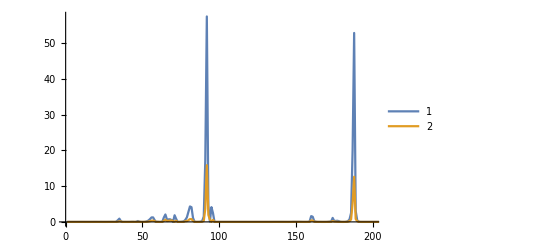

```mathematica
ListLinePlot[Table[(OμLHSEV.EvecsFEV[[-i]])^2,{i,1,2}],PlotRange->{{0,200},All},PlotLegends->Automatic]
```

```mathematica
Do[ev=OμLHSEV.EvecsFEV[[-i]];Print[{i,EvalsFEV[[-i]]},": ",{ev[[ind1]].nrm1.ev[[ind1]],ev[[ind2]].nrm2.ev[[ind2]],ev[[ind3]].nrm3.ev[[ind3]]}],{i,3,4}]
```

{3,1.65707}: {0.96846,0.0158294,0.015711}

{4,1.80677}: {0.984607,0.00779776,0.00759493}

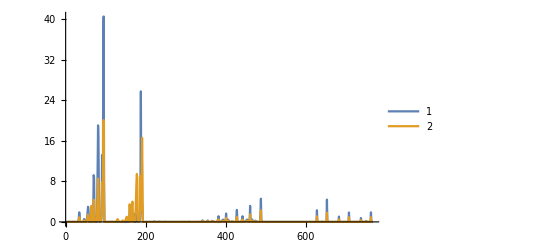

```mathematica
ListLinePlot[Table[(OμLHSEV.EvecsFEV[[-i]])^2,{i,3,4}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Do[ev=OμLHSEV.EvecsFEV[[-i]];Print[{i,EvalsFEV[[-i]]},": ",{ev[[ind1]].nrm1.ev[[ind1]],ev[[ind2]].nrm2.ev[[ind2]],ev[[ind3]].nrm3.ev[[ind3]]}],{i,5,8}]
```

{5,2.74631}: {0.995658,0.00189209,0.00245019}

{6,3.53924}: {0.0211385,0.00379089,0.975071}

{7,3.91075}: {0.959238,0.0115797,0.0291822}

{8,4.44485}: {0.0586037,0.000387972,0.941008}

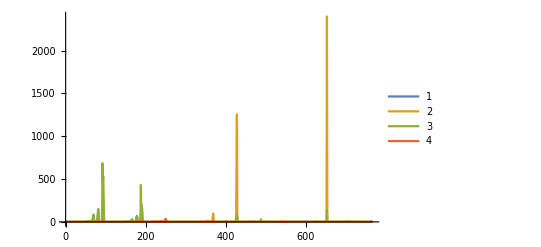

```mathematica
ListLinePlot[Table[(OμLHSEV.EvecsFEV[[-i]])^2,{i,5,8}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Do[ev=OμLHSEV.EvecsFEV[[-i]];Print[{i,EvalsFEV[[-i]]},": ",{ev[[ind1]].nrm1.ev[[ind1]],ev[[ind2]].nrm2.ev[[ind2]],ev[[ind3]].nrm3.ev[[ind3]]}],{i,9,10}]
```

{9,4.50674}: {0.930451,0.00803469,0.0615145}

{10,4.83502}: {0.413377,0.000419299,0.586203}

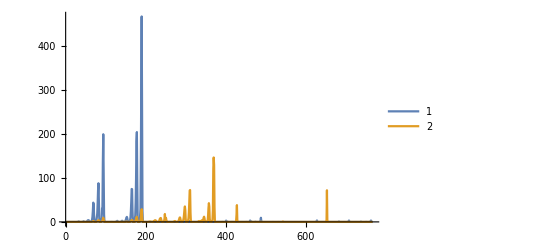

```mathematica
ListLinePlot[Table[(OμLHSEV.EvecsFEV[[-i]])^2,{i,9,10}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Do[ev=OμLHSEV.EvecsFEV[[-i]];Print[{i,EvalsFEV[[-i]]},": ",{ev[[ind1]].nrm1.ev[[ind1]],ev[[ind2]].nrm2.ev[[ind2]],ev[[ind3]].nrm3.ev[[ind3]]}],{i,11,20}]
```

{11,4.97504}: {0.529485,0.00113416,0.469381}

{12,5.14972}: {0.0588935,0.00345503,0.937651}

{13,5.29283}: {0.00093174,0.155592,0.843476}

{14,5.35159}: {0.0806604,0.773128,0.146211}

{15,5.41159}: {0.84625,0.1421,0.0116507}

{16,5.48509}: {0.13992,0.186128,0.673952}

{17,5.53892}: {0.135157,0.73117,0.133673}

{18,5.60232}: {0.752305,0.00824854,0.239446}

{19,5.84099}: {0.055511,0.0128648,0.931624}

{20,6.02697}: {0.861825,0.105211,0.0329643}

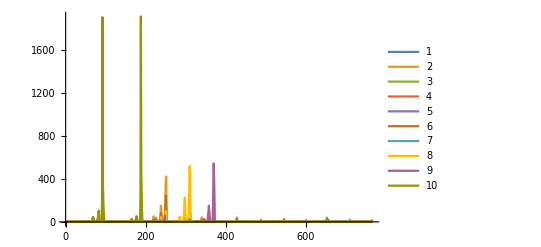

```mathematica
ListLinePlot[Table[(OμLHSEV.EvecsFEV[[-i]])^2,{i,11,20}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
seq1={{1,192},
```

```mathematica
LitNorm[{1:
```

```mathematica
{{1,192}->1,{193,252}->2,{253,312}->3,{313,432}->4,{433,492}->5,{493,547}->6,{548,602}->7,{603,657}->8,{658,767}->9}
```

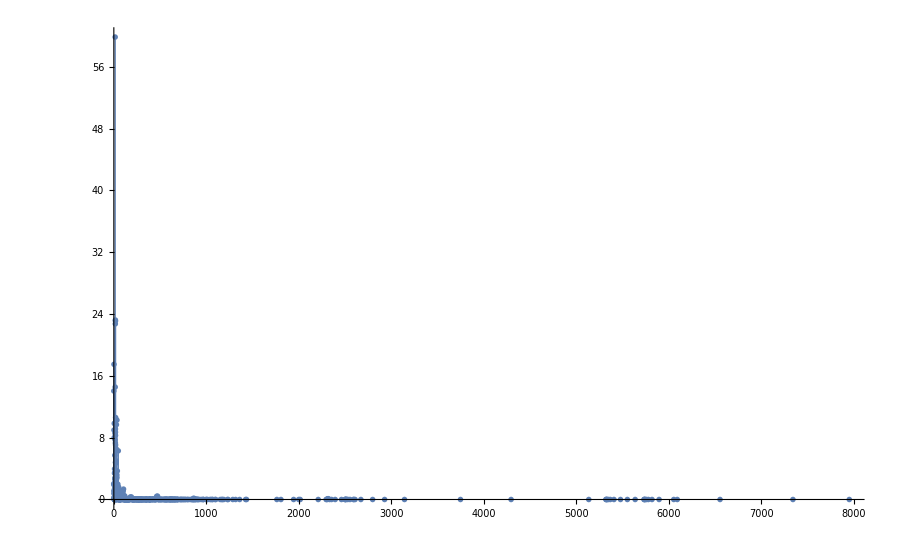
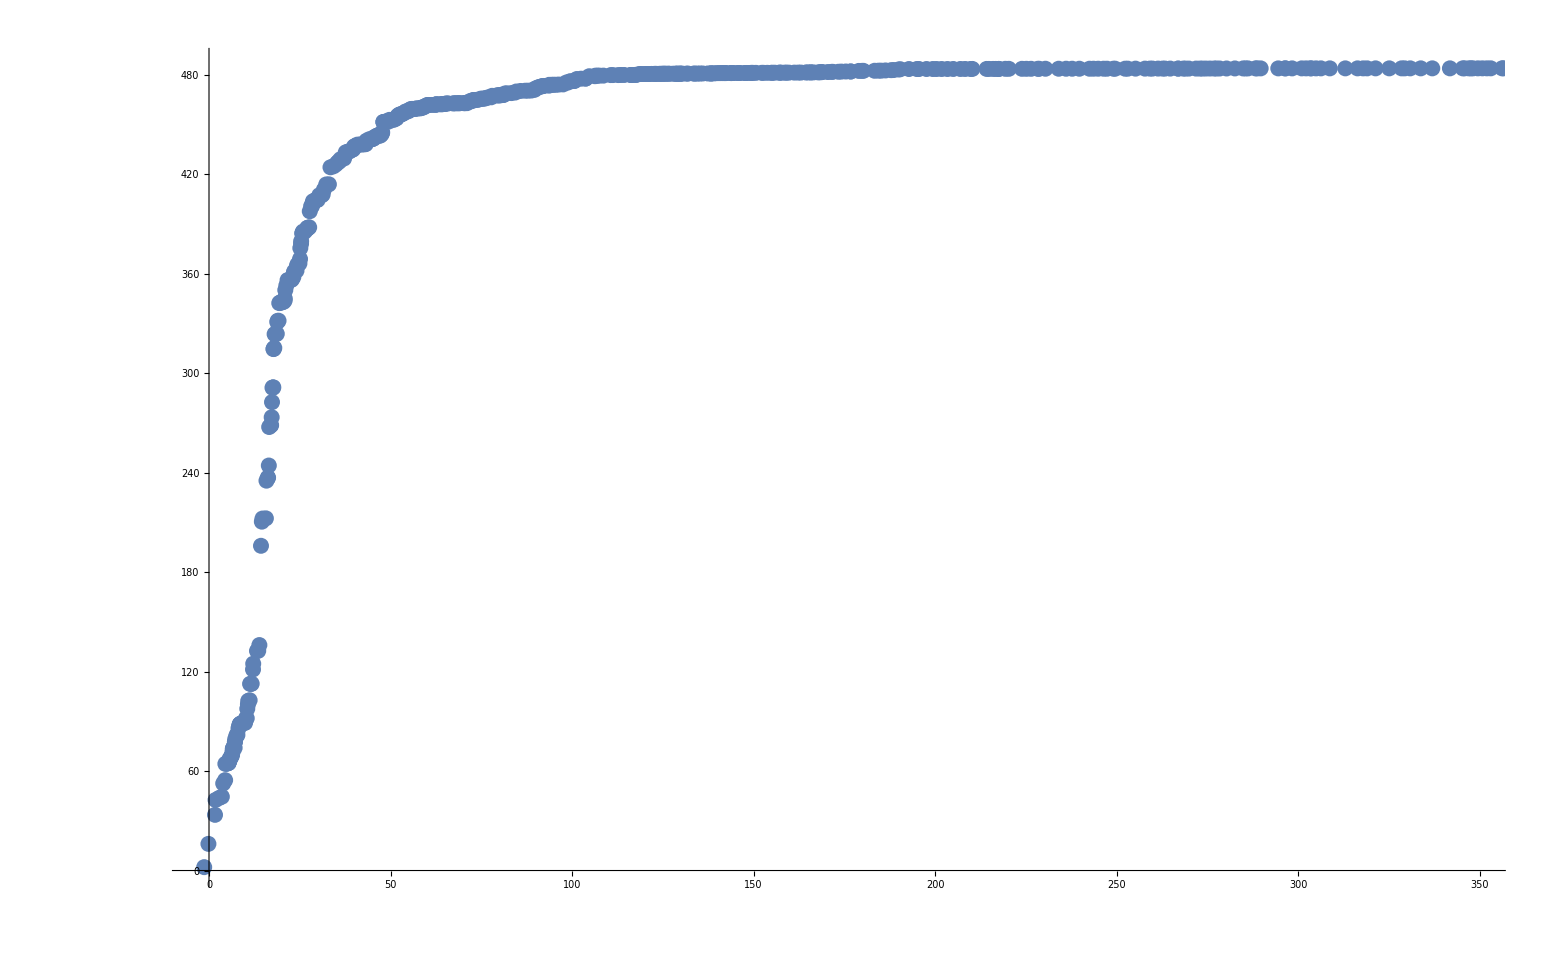
Grid[{-Graphics-,-Graphics-}]

Defficient LHS ME's: {583965}

Defficient RHS ME's: {185512}

```mathematica
plote3=Grid[{
ListPlot[Reverse[lpsisEV[[1]]],Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
,
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
}]
Print["Defficient LHS ME's: ",Dimensions[Select[Flatten[Chop[OμLHSEV.Transpose[OμLHSEV]]],#≠0.&&#≠1.&]]];
Print["Defficient RHS ME's: ",Dimensions[Select[Flatten[Chop[OμRHSEV.Transpose[OμRHSEV]]],#≠0.&&#≠1.&]]];
```

```mathematica
OrderedSpectF[[-11;;]]
```

{4.97504,4.83502,4.50674,4.44485,3.91075,3.53924,2.74631,1.80677,1.65707,-0.15842,-1.32485}

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengthsEV,LocalObject["CumHelionStrengths_"<>StringTake[resultsDir,{-11,-9}]]]
```

LocalObject[file:///home/niels/.Wolfram/Objects/CumHelionStrengths_v24]

```mathematica
suffies={"v18","v19","v20","v21","v22"};
CumStrengthS={};
Do[
AppendTo[CumStrengthS,Flatten[Get[LocalObject["CumHelionStrengths_"<>suff]],1]];
,{suff,suffies}
]

ListPlot[CumStrengthS,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,50},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotLegends->suffies]
```

LocalObject::nso: LocalObject[file:///home/niels/.Wolfram/Objects/CumHelionStrengths_v18] not found.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

LocalObject::nso: LocalObject[file:///home/niels/.Wolfram/Objects/CumHelionStrengths_v19] not found.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

LocalObject::nso: LocalObject[file:///home/niels/.Wolfram/Objects/CumHelionStrengths_v20] not found.

General::stop: Further output of LocalObject::nso will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1.].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

-Graphics-